```mathematica
CenterOfGravity[dataset_Dataset, xColumn_, yColumn_] :=
Block[{xyColumns, values, polygon},
xyColumns = dataset[All, {xColumn, yColumn}];
values= Values[xyColumns] // Normal;
polygon = WindingPolygon[values];
RegionCentroid[polygon]
]
```

```mathematica
MeanDistanceFromCenter[dataset_Dataset, xColumn_, yColumn_, center_] :=
Block[{xyColumns,values, allDistances},
xyColumns = dataset[All, {xColumn, yColumn}];
values = Values[xyColumns];
allDistances = Table[ArcLength[Line[{{values[x][1], values[x][2]}, center}]], {x, 1, Length[values], 1}];
Mean[allDistances]
]
```

```mathematica
GroupedMeanDistanceFromCenter[dataset_Dataset, xColumn_, yColumn_, center_, index_] :=
Block[{grouped},
grouped = dataset[GroupBy[index]];
Table[
MeanDistanceFromCenter[grouped[x], xColumn, yColumn, center],
{x, 1, Length[grouped], 1}
]
]
```

```mathematica
MeanDistancesFromCenter[dataset_Dataset, xColumn_, yColumn_, index_] :=
Block[{center},
center = CenterOfGravity[dataset, xColumn, yColumn];
GroupedMeanDistanceFromCenter[dataset, xColumn, yColumn, center, index]
]
```

```mathematica
truthData1=Import["~/workspace/PBLL/LieDetector/Analysis/truth.csv","Dataset","HeaderLines"->1]
```

Dataset[<>]

```mathematica
truthDistances1 = MeanDistancesFromCenter[truthData1, "Combine Gaze X", "Combine Gaze Y", "Index"]
```

{0.0275894,0.0185101,0.0250316,0.013946,0.0203309,0.01075,0.0185113,0.0185278,0.0125362,0.0110734,0.0182229,0.0137394,0.010763,0.0137315,0.0102101}

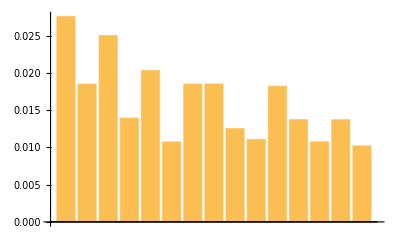

```mathematica
BarChart[truthDistances]
```

```mathematica
liesData1=Import["~/workspace/PBLL/LieDetector/Analysis/lies.csv","Dataset","HeaderLines"->1]
```

Dataset[<>]

```mathematica
liesDistances1 = MeanDistancesFromCenter[liesData1, "Combine Gaze X", "Combine Gaze Y", "Index"]
```

{0.0799216,0.0789666,0.0802236,0.0796856,0.0891261,0.087463,0.075667,0.0903439,0.0921123,0.094141,0.084547,0.0975595,0.0951323,0.0991249,0.0920381}

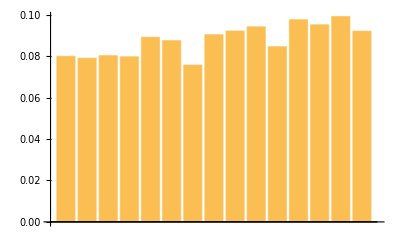

```mathematica
BarChart[liesDistances1]
```

```mathematica
PairedBarChart[truthDistances1, liesDistances1]
```

-Graphics-